```mathematica
<<MaTeX`
Get[FileNameJoin[{NotebookDirectory[],"SWNf1QuiverScattering.m"}]]
```

SWNf1QuiverScattering 1.1, Aug 2026 - Generic quiver scattering diagrams machinery

CoulombHiggs 6.3 - A package for evaluating quiver invariants

```mathematica
(* checks *)
```

```mathematica
Coll1={{0,1,1/2},{1,0,-1},{1,-1,1/2}};
Outer[DSZ, Coll1, Coll1, 1]-Mat
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Mat
(*expect {{0,-1,-1},{1,0,-1},{1,1,0}}*)

McKayDSZ[{1,0,0},{0,1,0}]   (*expect-1*)
McKayDSZ[{1,0,0},{0,0,1}]   (*expect-1*)
McKayDSZ[{0,1,0},{0,0,1}]   (*expect-1*)

McKayIntersectRays[{1,0,0},{0,1,0},0]   (*expect {0,0}*)
McKayIntersectRays[{1,0,0},{0,0,1},0]   (*expect {0,-1}*)
McKayIntersectRays[{0,1,0},{0,0,1},0]   (*expect {1,0}*)
```

{{0,-1,-1},{1,0,-1},{1,1,0}}

-1

-1

-1

{-1/6,-1/(2 √3)}

{1/3,0}

{-1/6,1/(2 √3)}

```mathematica
zet={1/3-u+Sqrt[3]v, -1/3-2u,1/3-u-Sqrt[3]v}
zet[[1]]-zet[[2]]+zet[[3]]
```

{1/3-u+√3 v,-1/3-2 u,1/3-u-√3 v}

1

{{u→1/3 (1+3 √3 v)},{u→-1/6},{u→1/3 (1-3 √3 v)}}

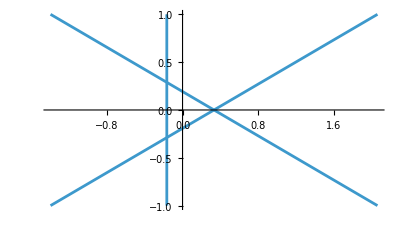

```mathematica
First[Solve[#==0,u]]&/@zet
ParametricPlot[{u,v}/.%, {v,-1,1}]
```

Adding 3 rays,

Adding 6 rays,

Adding 4 rays,

16 in total.

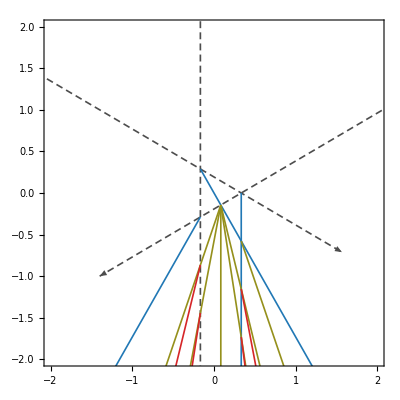

```mathematica
ListRaysTest = ConstructMcKayDiagram[15,5,0,{}];
Show[McKayPlotDiagram[ListRaysTest,0,"UseMaTeX"->False,"LabelMode"->"Tooltip"], PlotRange->{{-2,2},{-2,2}}]
```